```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3+Subscript[c, 0,4] x^4, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3+Subscript[c, 1,4](x-1)^4, 1<x≤2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3+Subscript[c, 2,4](x-2)^4, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 0,4],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 1,4],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3],Subscript[c, 2,4]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)

c_(1,1)+c_(1,2)+c_(1,3)+c_(1,4)

c_(2,1)+c_(2,2)+c_(2,3)+c_(2,4)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-2)^3 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-2)^3 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)+c_(1,1)+c_(1,2)+c_(1,3)+c_(1,4)+c_(2,1)+c_(2,2)+c_(2,3)+c_(2,4),-2 c_(0,2)-3 c_(0,3)-4 c_(0,4)-2 c_(1,2)-3 c_(1,3)-4 c_(1,4)-2 c_(2,2)-3 c_(2,3)-4 c_(2,4),2 c_(0,2)+3 c_(0,3)+6 c_(0,4)+2 c_(1,2)+3 c_(1,3)+4 c_(1,4)+2 c_(2,2)+3 c_(2,3)+4 c_(2,4)+2 (c_(1,4)+c_(2,4)),-4 c_(0,4)-4 (c_(1,4)+c_(2,4)),2 c_(0,4)+2 (c_(1,4)+c_(2,4))}

{1+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)+2 c_(1,1)+2 c_(1,2)+2 c_(1,3)+2 c_(1,4)+3 c_(2,1)+3 c_(2,2)+3 c_(2,3)+3 c_(2,4),-c_(0,1)-2 c_(0,2)-3 c_(0,3)-4 c_(0,4)-3 c_(1,1)-4 c_(1,2)-6 c_(1,3)-8 c_(1,4)-5 c_(2,1)-6 c_(2,2)-9 c_(2,3)-12 c_(2,4),c_(0,2)+3 c_(0,3)+6 c_(0,4)+c_(1,2)+6 c_(1,3)+12 c_(1,4)+c_(2,2)+9 c_(2,3)+18 c_(2,4),-c_(0,3)-4 c_(0,4)-3 c_(1,3)-8 c_(1,4)-5 c_(2,3)-12 c_(2,4),c_(0,4)+c_(1,4)+c_(2,4)}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,4)→-1-c_(0,1)-c_(0,2)-c_(0,3),c_(1,4)→-c_(1,1)-c_(1,2)-c_(1,3),c_(2,1)→-9/5-(9 c_(0,1))/5-(4 c_(0,2))/5-(2 c_(0,3))/5-(7 c_(1,1))/5-(2 c_(1,2))/5-(c_(1,3))/5,c_(2,2)→12/5+(12 c_(0,1))/5+(7 c_(0,2))/5+(6 c_(0,3))/5+(6 c_(1,1))/5+(c_(1,2))/5+(3 c_(1,3))/5,c_(2,3)→-8/5-(8 c_(0,1))/5-(8 c_(0,2))/5-(9 c_(0,3))/5-(4 c_(1,1))/5-(4 c_(1,2))/5-(7 c_(1,3))/5,c_(2,4)→1+c_(0,1)+c_(0,2)+c_(0,3)+c_(1,1)+c_(1,2)+c_(1,3)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]
```

{{-2,3},{-2,2},{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2},{3,-2},{3,-3}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/2646000000(14670634896 c_(0,1)^4+606507296 c_(0,2)^4+4 c_(0,2)^3 (1949851966+232907098 c_(0,3)+617124018 c_(1,1)+290282568 c_(1,2)+113366709 c_(1,3))+6 c_(0,1)^3 (14010589344+4372344264 c_(0,2)+1641040132 c_(0,3)+4483994112 c_(1,1)+2032526862 c_(1,2)+769025431 c_(1,3))+4 c_(0,2)^2 (9167147804+136084136 c_(0,3)^2+1130374116 c_(1,1)^2+2879113734 c_(1,2)+253899816 c_(1,2)^2+1129878642 c_(1,3)+201470916 c_(1,2) c_(1,3)+40742529 c_(1,3)^2+6 c_(1,1) (1009302314+175412672 c_(1,2)+68040261 c_(1,3))+c_(0,3) (2240602399+707391852 c_(1,1)+337352727 c_(1,2)+133865301 c_(1,3)))+2 c_(0,1)^2 (8840566888 c_(0,2)^2+3 c_(0,2) (18937165782+2227535596 c_(0,3)+6036848586 c_(1,1)+2766513536 c_(1,2)+1057275843 c_(1,3))+3 (29453209136+427108874 c_(0,3)^2+3668896144 c_(1,1)^2+9157188606 c_(1,2)+785922744 c_(1,2)^2+3522204753 c_(1,3)+609222194 c_(1,2) c_(1,3)+120391136 c_(1,3)^2+c_(0,3) (7159760466+2272854293 c_(1,1)+1053419843 c_(1,2)+409158534 c_(1,3))+2 c_(1,1) (9864820428+1674943894 c_(1,2)+636803947 c_(1,3))))+3 c_(0,2) (47722966 c_(0,3)^3+c_(0,3)^2 (1161284166+365577168 c_(1,1)+176751868 c_(1,2)+71148259 c_(1,3))+4 c_(0,3) (2345936743+287776097 c_(1,1)^2+66491972 c_(1,2)^2+294016014 c_(1,3)+11009318 c_(1,3)^2+c_(1,2) (737796028+53640772 c_(1,3))+c_(1,1) (1536686753+271200644 c_(1,2)+106899522 c_(1,3)))+2 (11971578004+675849468 c_(1,1)^3+70686368 c_(1,2)^3+2452696513 c_(1,3)+174072637 c_(1,3)^2+4683721 c_(1,3)^3+4 c_(1,2)^2 (275830787+21080513 c_(1,3))+c_(1,1)^2 (4931450498+933464704 c_(1,2)+358152902 c_(1,3))+4 c_(1,2) (1552337394+217117737 c_(1,3)+8535469 c_(1,3)^2)+2 c_(1,1) (6452849063+219512052 c_(1,2)^2+887904374 c_(1,3)+34001388 c_(1,3)^2+24 c_(1,2) (95773077+7135123 c_(1,3)))))+3 (4761552 c_(0,3)^4+c_(0,3)^3 (152378486+47832803 c_(1,1)+23442953 c_(1,2)+9559314 c_(1,3))+c_(0,3)^2 (1838434268+223352272 c_(1,1)^2+53063372 c_(1,2)^2+232070089 c_(1,3)+9034718 c_(1,3)^2+8 c_(1,2) (71850441+5430284 c_(1,3))+4 c_(1,1) (296799357+53253461 c_(1,2)+21295618 c_(1,3)))+2 c_(0,3) (4578199952+255032734 c_(1,1)^3+27775484 c_(1,2)^3+963184594 c_(1,3)+68786356 c_(1,3)^2+1921098 c_(1,3)^3+c_(1,2)^2 (426450074+33670276 c_(1,3))+2 c_(1,1)^2 (940428212+178028451 c_(1,2)+69391638 c_(1,3))+c_(1,2) (2388891813+339841674 c_(1,3)+13828463 c_(1,3)^2)+c_(1,1) (4908499263+169697152 c_(1,2)^2+691507224 c_(1,3)+27092213 c_(1,3)^2+4 c_(1,2) (441331037+33628038 c_(1,3))))+2 (8398194146+515187536 c_(1,1)^4+25077936 c_(1,2)^4+2464110641 c_(1,3)+299371476 c_(1,3)^2+12762541 c_(1,3)^3+715571 c_(1,3)^4+16 c_(1,2)^3 (12495433+2510042 c_(1,3))+4 c_(1,1)^3 (475525332+234610286 c_(1,2)+89137143 c_(1,3))+4 c_(1,2)^2 (457033426+59089098 c_(1,3)+6143001 c_(1,3)^2)+2 c_(1,2) (3129991691+730471427 c_(1,3)+47272023 c_(1,3)^2+3397734 c_(1,3)^3)+2 c_(1,1)^2 (3892323052+325618808 c_(1,2)^2+508337521 c_(1,3)+49153852 c_(1,3)^2+6 c_(1,2) (220602207+41805493 c_(1,3)))+2 c_(1,1) (6514031816+102643472 c_(1,2)^3+1438433027 c_(1,3)+96382698 c_(1,3)^2+6500334 c_(1,3)^3+4 c_(1,2)^2 (156318698+30155377 c_(1,3))+c_(1,2) (3693303104+486877442 c_(1,3)+48105554 c_(1,3)^2))))+c_(0,1) (5327710384 c_(0,2)^3+8 c_(0,2)^2 (6430478624+760812647 c_(0,3)+2041482552 c_(1,1)+946942227 c_(1,2)+365697726 c_(1,3))+12 c_(0,2) (13370089136+195939849 c_(0,3)^2+1652893894 c_(1,1)^2+4188688556 c_(1,2)+361115344 c_(1,2)^2+1627882803 c_(1,3)+282820644 c_(1,2) c_(1,3)+56455961 c_(1,3)^2+c_(0,3) (3263400916+1032163643 c_(1,1)+484753168 c_(1,2)+190235484 c_(1,3))+2 c_(1,1) (4457455803+760915944 c_(1,2)+291922897 c_(1,3)))+3 (102225866 c_(0,3)^3+c_(0,3)^2 (2523364016+794313468 c_(1,1)+377723568 c_(1,2)+150391009 c_(1,3))+4 c_(0,3) (5088150143+624378947 c_(1,1)^2+139825522 c_(1,2)^2+632780814 c_(1,3)+22546868 c_(1,3)^2+c_(1,2) (1601822453+111309522 c_(1,3))+c_(1,1) (3375005903+581045794 c_(1,2)+226491672 c_(1,3)))+2 (26226201004+1504735968 c_(1,1)^3+151476568 c_(1,2)^3+5238604963 c_(1,3)+376306612 c_(1,3)^2+9655171 c_(1,3)^3+96 c_(1,2)^2 (24990338+1858287 c_(1,3))+2 c_(1,1)^2 (5396154124+1030280202 c_(1,2)+391850101 c_(1,3))+2 c_(1,2) (6719150063+940706774 c_(1,3)+35651988 c_(1,3)^2)+4 c_(1,1) (7095622594+239418376 c_(1,2)^2+962474362 c_(1,3)+36326769 c_(1,3)^2+c_(1,2) (2504575249+184853551 c_(1,3)))))))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
NSols=NSolve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[NSols]],Err/.NSols,PositiveDefiniteMatrixQ[H/.N[#]]&/@NSols}ᵀ]
```

1 | 0.029495 | True

{c_(0,4)→0.0338547,c_(1,4)→0.0165229,c_(2,1)→0.10093,c_(2,2)→-0.00915814,c_(2,3)→-0.0413939,c_(2,4)→-0.0503776,c_(0,1)→-0.443271,c_(0,2)→-0.70886,c_(0,3)→0.118277,c_(1,1)→-0.54828,c_(1,2)→0.389883,c_(1,3)→0.141874}

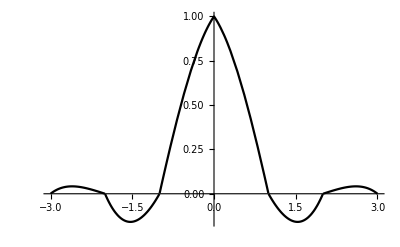

```mathematica
NSol=NSols[[1]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```